# XX: Iterative Methods What, Why, and When

Almost all of the algorithms so far have operated on the matrix entries.  These algorithms have typically performed a length m loop loop through all m^2 entries of an m×m square matrix.  They have all required storing a (hopefully small multiple of m^2) entries: our in place algorithms are an attempt to be careful about memory use. They have all required a multiple of m^3 arithmetic operations: our blocked algorithms using the built-in matrix-matrix and matrix-vector operations are an attempt to do this efficiently but there are still a multiple of m^3arithmetic operations.

Almost all large real world matrices inherit some special structure from the physics/engineering they describe.  For instance, almost all standard ways to convert systems of PDEs to linear algebra generate matrices that are almost all zeros: these are the sparse matrices that we have been seen in Mathematica, Julia, etc.

## PDE Discretization 1D: Finite Differences (FD)

Consider the standard PDE
	u_xx=f
on the domain x∈Ω=(0,a) with Dirichlet boundary conditions u|_(∂Ω)=0 on the boundary ∂Ω on the domain Ω.   The common differential operator Δu=∇^2 u=u_xx is called the 1D Laplacian.  A standard centered difference approximation is
	u_xx(x)=(u[x-h] - 2 u[x] + u[x+h])/h^2
If we pick n equally spaced internal points
	x_i=0+i h for i=1:n
with h=a/(n+1) then we can approximate the PDE by the set of linear equations
	(u[x_i-h] - 2 u[x_i] + u[x_i+h])/h^2=f[x_i] for i=1:n.
The internal discretization points get called nodes!
This looks a lot cleaner if we write u_i=u[x_i] and f_i=f[x_i] fro the nodal values and multiply through by h^2. This gives
	u_(i-1)-2 u_i+u_(i+1)=h^2 f_i for i=1:n
Now x_0=0 and x_(n+1)=0 so the Dirichlet boundary conditions say u_0=u_(n+1)=0. This makes the first i=1 and last i=n equations simpler. The first two linear equations are  
	-2 u_1 | + | u_2 | + | 0 u_3 | = | h^2 f_1
u_1 | - | 2 u_2 | + | u_3 | = | h^2 f_2
the generic middle equations are all the same
	u_(i-1)-2 u_i+u_(i+1)=h^2 f_i fori=2:n-1
and the last two equations are 
	u_(n-2) | - | 2 u_(n-1) | + | u_n | = | h^2 f_(n-1)
0 u_(n-2) | + | u_(n-1) | - | 2 u_n | = | h^2 f_n
Writing this as a matrix equation we get
	A.u=f
where A is the n×n symmetric tridiagonal matrix with -2 down the diagonal and 1 down the sub and supper diagonal.   It is not an accident that it is easy to define A and solve the discretized system A.u=f in every computational tool.	

Lets make up a problem that we know the answer to, build the system and look at the  and actually do this.

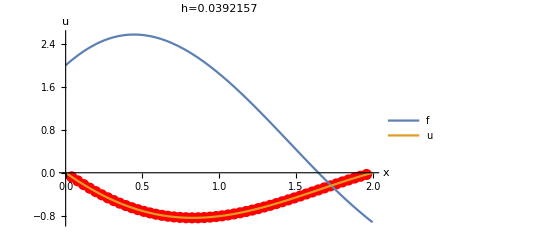

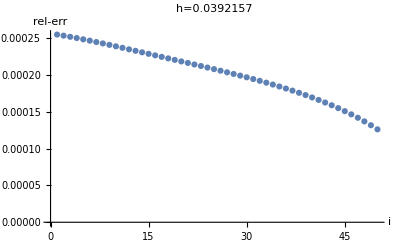

```mathematica
a=2;
uExact[x_]:= Cos[0.2x+0.1ArcTan[x]](x-a)Sin[x]
f[x_]=D[uExact[x],{x,2}];
n=50;
h=a/(n+1.0);
xs=Table[i h, {i,1,n}];
fs=f[xs];
m=n;
A=SparseArray[{
Band[{1,1}]->-2, 
Band[{1,2}]->1, 
Band[{2,1}]->1},{m,m}];
us=LinearSolve[A,h^2 fs];
Plot[{f[x],uExact[x]},{x,0,2},
AxesLabel->{"x","u"},
PlotLegends->{"f","u"},
PlotLabel->StringForm["h=``",h],
Prolog->{Red,PointSize[0.02],Point[{xs,us}ᵀ]}
]
ListPlot[Abs[(uExact[xs]-us)/uExact[xs]],
AxesLabel->{"i","rel-err"},
PlotLabel->StringForm["h=``",h]]
```

The eigenvalue problem (the minus sign is almost always inserted in this context)
	u_xx=-λ u
on the domain x∈Ω=(0,2) with Dirichlet boundary conditions u|_(∂Ω)=0 on the boundary ∂Ω on the domain Ω produces the same matrix since the discretization of the PDE is just
	(u[x_i-h] - 2 u[x_i] + u[x_i+h])/h^2=-λ u[x_i]
The eigenvectors of this matrix approximate standing waves of a guitar string and the eigenvalues determine the frequencies.

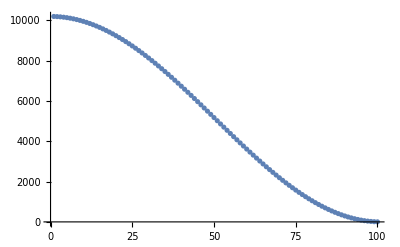

```mathematica
n=100;
h=a/(n+1.0);
m=n;
A=-1/h^2 SparseArray[{
Band[{1,1}]->-2.0, 
Band[{1,2}]->1, 
Band[{2,1}]->1},{n,n}];
{λs,Vs}=Eigensystem[A];
ListPlot[λs]
```

In this case it is the small eigenvalues that matter most physically.  This is what the matching eigenvectors look like.

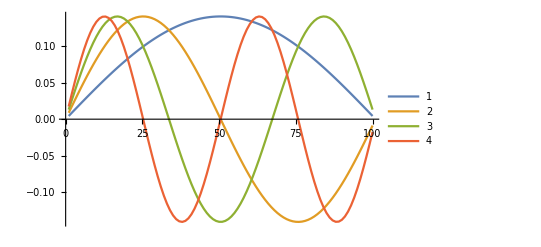

```mathematica
ListPlot[Vs⟦{-1,-2,-3,-4}⟧,
PlotLegends->Automatic,
Joined->True]
```

Math, Science, Engineering, and Musical folks all call these fundamental modes.

## PDE Discretization 2D: Finite Differences (FD)

Consider the Poisson PDE 
	u_xx+u_yy=f
on a rectangular domain Ω =(0,a)×(0,b) with Dirichlet boundary conditions u|_(∂Ω)=0. The common differential operator Δu=∇^2 u=u_xx+u_yy is called the Laplacian.  Standard centered difference approximations are
	u_xx[x,y]=(u[x- Δx,y] - 2 u[x,y] + u[x+Δx,y])/Δx^2 and u_yy[x,y]=(u[x,y-Δy] - 2 u[x,y] + u[x,y+Δy])/Δy^2 
Choose
	x_i=0+i Δx=i h for i  in 1 : n_1
	y_j=0+j Δy=j h for j in 1:n_2
with Δx=a/(n_1+1)  and Δy=b/(n_2+1) and define. Approximate the Poisson PDE by the set of linear equations
	(u[x_i-Δx,y_j] - 2 u[x_i,y_j] + u[x_i+Δx,y_j])/Δx^2+(u[x_(i,)y_j-Δy] - 2 u[x_i,y_j] + u[x_i+Δy,y_j])/Δy^2=f[x_i,y_j] for i  in 1:n_1 and j  in 1:n_2
This looks a lot cleaner if we write u_(i,j)=u[x_i,y_j], f_(i,j)=f[x_i,y_j] for the discretized field values. We have two different discretization lengths Δx and Δy.  It is usually good to have Δx≈Δy so we write Δy=Δx/γ and multiply through by Δx^2. This gives
	  |   | γ u_(i,j+1) |   |   |   |  
u_(i-1,j) | - | (2+2γ) u_(i,j) | + | u_(i+1,j) | = | Δx^2 f_(i,j)
  |   | γ u_(i,j-1) |   |   |   |  
The pattern above to approximate the Laplacian (particularly with γ=1)is called the standard 5 point stencil for the Laplacian.  The Dirichlet boundary conditions 
	u(0,y)=u(a,y)=u(x,0)=u(x,b)=0
simplify the “just-inside” i=j=1 and i=n_1and j=n_2 equations like before.  Here is a standard way to convert the block of equations into linear algebra. First number the n^2 interior nodes in some order.  Here is a standard very organized numbering scheme for this very regular mesh.

```mathematica
kFromij[{i_,j_},n1_]:=i+n1(j-1);
ijFromk[k_,n1_]:=Module[{i,j},
i=Mod[k,n1];j=1+(k-i)/n1;
{i,j}]
```

{0.275,0.3}

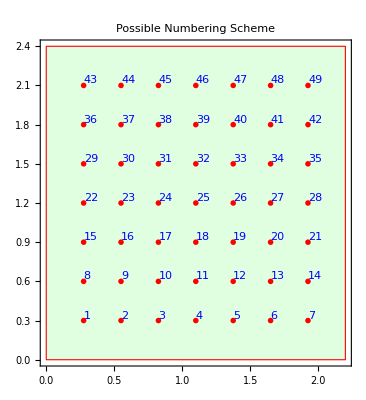

```mathematica
{a,b}={2.2,2.4};
{n1,n2}=Round[3{a,b}];
{Δx,Δy}={a/(n1+1.0),b/(n2+1.0)}
Graphics[ {
{LightGreen,EdgeForm[Red],Rectangle[{0,0},{a,b}]},
{PointSize[0.01],Table[{
{Red,Point[{i*Δx,j*Δy}]},
{Blue, Text[kFromij[{i,j},n1],{i*Δx,j*Δy},{-1,-1}]}},
{i,1,n1},{j,1, n2}]}
},
PlotLabel->"Possible Numbering Scheme",
Frame->True]
```

If I unwind the list of u_(i,j) and f_(i,j) values using this order I get vectors u_k and f_k of length with k in 1:m=n_1×n_2. The equations are going to become an m×m matrix A.   The interior {i,j} equations are 
		  |   | γ u_(i,j+1) |   |   |   |  
u_(i-1,j) | - | (2+2γ) u_(i,j) | + | u_(i+1,j) | = | Δx^2 f_(i,j)
  |   | γ u_(i,j-1) |   |   |   |  
The almost edge nodes i=j=1 and i=n_1 and j=n_2 are special because they are missing neighbours.   The almost corner nodes {i,j}={1,1}, {i,j}={1,n_2}, {i,j}={n_1,1}, and {i,j}={n_1,n_2} are missing two neighbours!  They are missing neighbours because the boundary conditions is that u=0 at the edge nodes i=0, j=0, i=n_(1+1), and j=n_2+1.

Rows of matrices are equations: each row of the matrix A encodes one of the equations above.

Most equations involve 5 variables.

The almost edge equations only involve 4 variables.

The 4 almost corner equations involve only 3 variables.

Columns of matrices match variables:

Most rows A have 5 non-zero entries.

The almost edge rows have 4 non-zeros

The 4 almost corner rows only have 3 non-zeros

There are lots of ways to build the matrix A.  One standard way (and one that extends directly to less-special domains and other ways of discretizing PDEs) is to just step through all the nodes (rows of the equation) inserting appropriate entries into A.

### PDE Matrix/Vector Build: Nodes

Lets build the RHS vector b from the function f with numbering scheme above for
	u_xx+u_yy=f[x,y]

```mathematica
{a,b}={2.2,2.4};
{n1,n2}=Round[20{a,b}];
{Δx,Δy}={a/(n1+1.0),b/(n2+1.0)};
γ=Δy/Δx;
f[x_,y_]:=-Exp[x+y^2]
m=n1*n2;
b=ConstantArray[0,m];
Do[k=kFromij[{i,j},n1];
b⟦k⟧=Δx^2 f[i*Δx,j*Δy],
{i,1,n1},{j,1,n2}]
ListPlot[b];
```

The idea for the matrix A is similar.

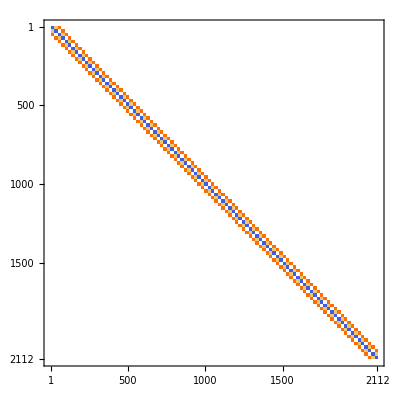

```mathematica
A=SparseArray[{},{m,m}];
(* Build the interior Eqs *)
Do[k=kFromij[{i,j},n1];
A⟦k,k⟧=-(2+2γ);
A⟦k,kFromij[{i-1,j},n1]⟧=1;
A⟦k,kFromij[{i+1,j},n1]⟧=1;
A⟦k,kFromij[{i,j-1},n1]⟧=γ;
A⟦k,kFromij[{i,j+1},n1]⟧=γ,
{i,2,n1-1},{j,2,n2-1}]
(* Build the almost edge Eqs *)
(* i=1 *)
Do[k=kFromij[{1,j},n1];
A⟦k,k⟧=-(2+2γ);
A⟦k,kFromij[{2,j},n1]⟧=1;
A⟦k,kFromij[{1,j-1},n1]⟧=γ;
A⟦k,kFromij[{1,j+1},n1]⟧=γ,
{j,2,n2-1}]
(* i=n1 *)
Do[k=kFromij[{n1,j},n1];
A⟦k,k⟧=-(2+2γ);
A⟦k,kFromij[{n1-1,j},n1]⟧=1;
A⟦k,kFromij[{n1,j-1},n1]⟧=γ;
A⟦k,kFromij[{n1,j+1},n1]⟧=γ,
{j,2,n2-1}]
(* j=1 *)
Do[
k=kFromij[{i,1},n1];
A⟦k,k⟧=-(2+2γ);
A⟦k,kFromij[{i-1,1},n1]⟧=1;
A⟦k,kFromij[{i+1,1},n1]⟧=1;
A⟦k,kFromij[{i,2},n1]⟧=γ,
{i,2,n1-1}]
(* j=n2 *)
Do[
k=kFromij[{i,n2},n1];
A⟦k,k⟧=-(2+2γ);
A⟦k,kFromij[{i-1,n2},n1]⟧=1;
A⟦k,kFromij[{i+1,n2},n1]⟧=1;
A⟦k,kFromij[{i,n2-1},n1]⟧=γ,
{i,2,n1-1}]
(* Build the almost corner Eqs *)
(* 1-1 *)
k=kFromij[{1,1},n1];
A⟦k,k⟧=-(2+2γ);
A⟦k,kFromij[{2,1},n1]⟧=1;
A⟦k,kFromij[{1,2},n1]⟧=γ;
(* n1-1 *)
k=kFromij[{n1,1},n1];
A⟦k,k⟧=-(2+2γ);
A⟦k,kFromij[{n1-1,1},n1]⟧=1;
A⟦k,kFromij[{n1,2},n1]⟧=γ;
(* 1-n2 *)
k=kFromij[{1,n2},n1];
A⟦k,k⟧=-(2+2γ);
A⟦k,kFromij[{2,n2},n1]⟧=1;
A⟦k,kFromij[{1,n2-1},n1]⟧=γ;
(* n1-n2 *)
k=kFromij[{n1,n2},n1];
A⟦k,k⟧=-(2+2γ);
A⟦k,kFromij[{n1-1,n2},n1]⟧=1;
A⟦k,kFromij[{n1,n2-1},n1]⟧=γ;
(* Lets look at what we have built *)
MatrixPlot[A]
```

```mathematica
MatrixForm[A⟦1;;20,1;;20⟧]
```

(-4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4.00371)

Lets solve and plot the solution of our linear system

```mathematica
u=LinearSolve[A,b];
ListPlot[u];
ListPlot3D[Partition[u,n1]]
```

-Graphics3D-

The eigenvalue problem 
	u_xx+u_yy=λ u
translates directly into an eigenvalue problem for our matrix A scaled by Δx^2. As before the small eigenvalues are the interesting ones here. When reinterpreted back onto the nodes the “smallest” eigenvectors are the fundamental modes.

Eigensystem::arh: Because finding 2112 out of the 2112 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

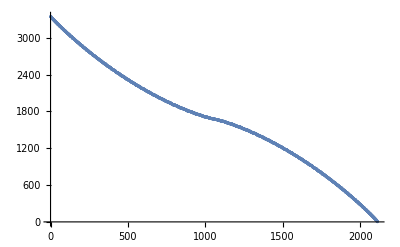

123456

```mathematica
{λs,vs}=Eigensystem[-A/Δx^2];
ListPlot[λs]
TabView[Map[ListPlot3D[Partition[#,n1]]&,{vs⟦-1⟧,vs⟦-2⟧,vs⟦-3⟧,vs⟦-4⟧,vs⟦-5⟧,vs⟦-6⟧}]]
```

### PDE Matrix/Vector Build: Kronecker Products

There are other more ways to build these matrices. First it would be nice to leave the u values as a matrix.  We know that doing stuff on one side does row ops and doing stuff on the other side does column ops. Writing U for the n_1×n_2 block of U_(i,j)≈u(x_i,y_j) and F_(i,j)=f(x_i,y_j) our PDE is 
	L_1.U+γ U.L_2=Δx^2 F
where L_1 is the n_1×n_1 symmetric tridiagonal matrix with -2 on the diagonal and 1 on the off diagonals and L_2 is the n_2×n_2 equivalent. This is called a Sylvester matrix equation if you are in math and not Russian. Russians and electrical engineers call it a Lyapunov equation.  The Mathematica command is LyapunovSolve.

```mathematica
?LyapunovSolve
```

The solution is of course the same.

```mathematica
LMat[n_]:= SparseArray[{Band[{1,1}]->-2,Band[{1,2}]->1,Band[{2,1}]->1},{n,n}]
F=Table[f[i Δx,j Δy],{i,1,n1},{j,1,n2}];
U=LyapunovSolve[LMat[n1],γ LMat[n2],Δx^2 F];
ListPlot3D[U]
```

-Graphics3D-

It possible to build the big m×m matrix (remember m=n1×n2) out of these smaller matrices. Our tick to turn vector into matrices by numbering along the rows and then down the column is a single Mathematica (or matlab or Julia) command “Flatten”. The “vector trick” is just that Flatten[A.X.B]=(A⊗Bᵀ).Flatten[X]. There is no real content here

```mathematica
{n1,n2,n3,n4}={2,4,5,2};
{A,X,B}=Map[RandomReal[{-1,1},#]&,
{{n1,n2},{n2,n3},{n3,n4}}];
AXB=A.X.B
KroneckerProduct[A,Bᵀ].Flatten[X]
Flatten[AXB]
```

{{-0.851879,-0.0816659},{1.35405,1.0446}}

{-0.851879,-0.0816659,1.35405,1.0446}

{-0.851879,-0.0816659,1.35405,1.0446}

Writing our Lyapunov version of the PDE
	U.L_2+γ L_1.U=Δx^2 F
as
	 I_1.U.L_2+γ L_1.U.I_2=Δx^2 F
we can see that it is equivalent to 
	(I_1⊗(L_2)ᵀ+γ(L_1⊗(I_2)ᵀ).vec(U)=Δx^2 vec(F)
In other words the matrix we worked so hard to build in the original version is simply

```mathematica
Clear[γ]
{n1,n2}={5,6};
A=KroneckerProduct[IdentityMatrix[n1],LMat[n2]ᵀ]+γ KroneckerProduct[LMat[n1],IdentityMatrix[n2]ᵀ]
MatrixForm[A];
```

SparseArray[…]